Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210324_disc_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

```mathematica
data=Table[Take[datafull,UpTo@i],{i,{39871,79567,118358,158421,198041,237352,277147,316411,356385,396096}}];
```

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

Investigation of Constraints Impact in Time Windows

Modularity Algorithms

Girvan & Newman Modularity

M.E.J.Newman, Modularity and community structure in networks (2006).

```mathematica
,
```

```mathematica
,
```

```mathematica
GirvanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q,div1,div2,moditer,r1,r11,r12,r2,r21,r22,subfinal1Q,subfinal2Q,finalQ},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x≥0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β][[1]]]])^2,{i,VertexList@network}]*β))/(4*m);
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Positive];
moditer[pos_,B1_]:=Module[{Bg,ug,βg,sg,deltaQ,divv1,divv2,Bg1,Bg2},
Bg=(Table[B1[[i,j]]-KroneckerDelta[i,j]*Total@B1[[i,pos]],{i,Length@B1},{j,Length@B1}])[[pos,pos]];
ug=Eigenvectors@Bg;
βg=Eigenvalues@Bg;
sg=(ug/.x_/;x<0->-1)/.x_/;x≥0->1;
deltaQ=(Total@(Table[(ug[[i]].Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]])^2,{i,Range@Length@pos}]*βg))/(4*m);
divv1=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Negative];
divv2=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Positive];{deltaQ,divv1,divv2,Bg}];
r1=moditer[div1,B];
r11=If[r1[[1]]>0.001,moditer[r1[[2]],r1[[4]]],{0,0,0,0}];
r12=If[r1[[1]]>0.001,moditer[r1[[3]],r1[[4]]],{0,0,0,0}];
r2=moditer[div2,B];
r21=If[r2[[1]]>0.001,moditer[r2[[2]],r2[[4]]],{0,0,0,0}];
r22=If[r2[[1]]>0.001,moditer[r2[[3]],r2[[4]]],{0,0,0,0}];
subfinal1Q=If[r1[[1]]>0.001,If[r11[[1]]>0.001,If[r12[[1]]>0.001,r12[[1]]+r11[[1]]+r1[[1]],r11[[1]]+r1[[1]]],If[r12[[1]]>0.001,r12[[1]]+r1[[1]],r1[[1]]]],0];
subfinal2Q=If[r2[[1]]>0.001,If[r21[[1]]>0.001,If[r22[[1]]>0.001,r22[[1]]+r21[[1]]+r2[[1]],r21[[1]]+r2[[1]]],If[r22[[1]]>0.001,r22[[1]]+r2[[1]],r2[[1]]]],0];
finalQ=Q+subfinal1Q+subfinal2Q]
```

Assortativity Modularity (Wolfram)

where m is the number of edges,
A is the adjacency matrix,
 is the degree of node i,
 is the community that node i belongs to, 
 is the Kronecker δ symbol. 

For weighted graphs, 
A is the weighted adjacency matrix, 
 are the sum of weights of edges incident on node i,
m is the sum of all weights.

```mathematica
GraphAssortativity[graph,communities,"Normalized"->False]
```

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,11,10];]
```

{310.896,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

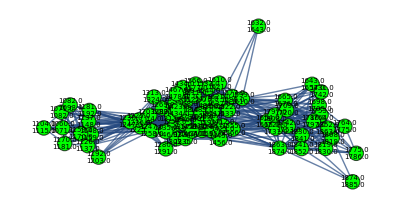
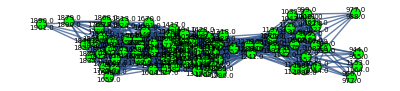
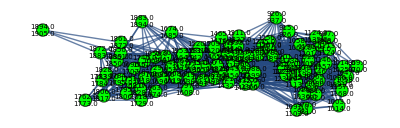
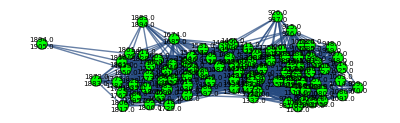
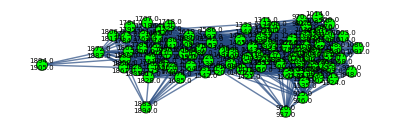
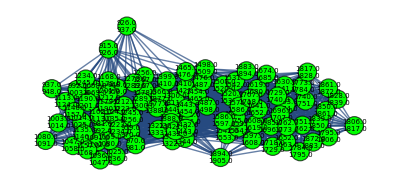
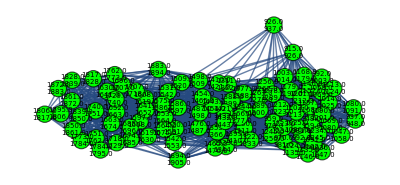
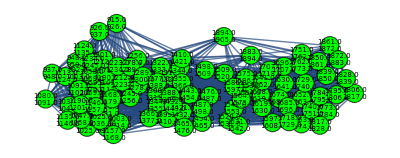
{{-Graphics-,71},{-Graphics-,85},{-Graphics-,90},{-Graphics-,90},{-Graphics-,90},{-Graphics-,90},{-Graphics-,90},{-Graphics-,90},{-Graphics-,90},{-Graphics-,91}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{297.445,{{36.0974,42.4864,-20.7875},{52.4337,58.0168,-51.6593},{43.2822,50.6385,-50.4871},{51.3002,57.3153,-52.5093},{57.4549,64.5,-48.3398},{53.1364,59.114,-59.6581},{55.8129,60.2327,-63.0283},{60.5327,67.3358,-54.2497},{62.078,68.8548,-58.9024},{66.098,68.9007,-45.6631}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,2,2,2,2,2,3,2,3}

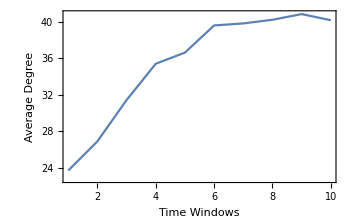
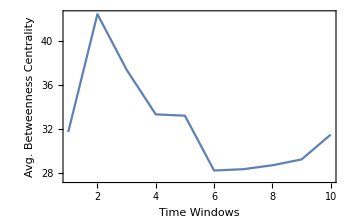
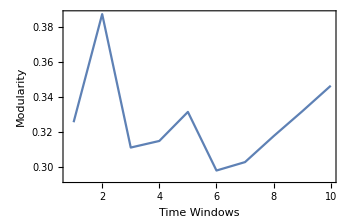
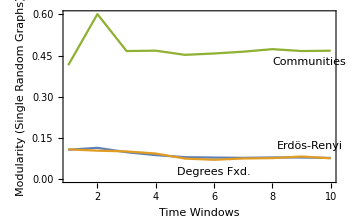
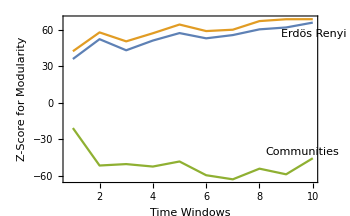

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,1,10];]
```

{124.023,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

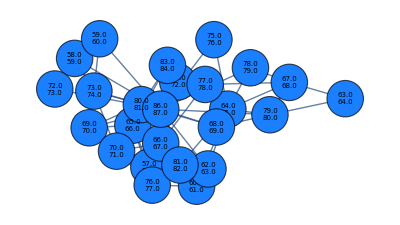
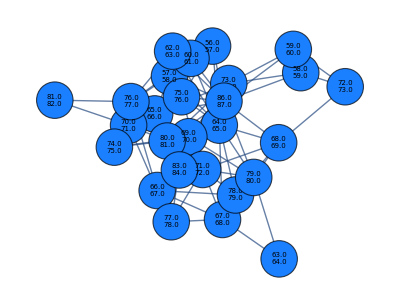
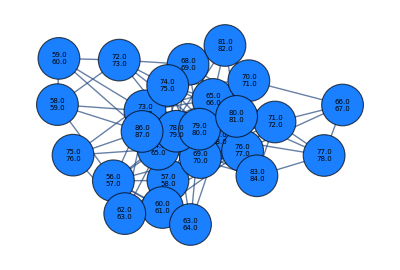
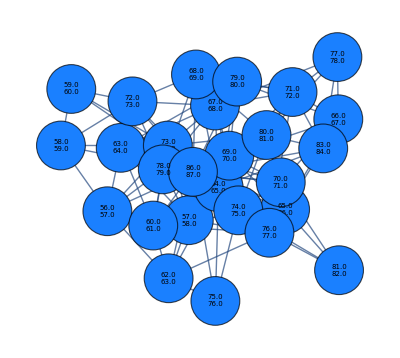
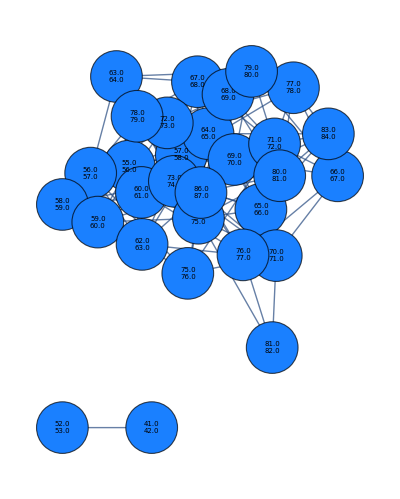
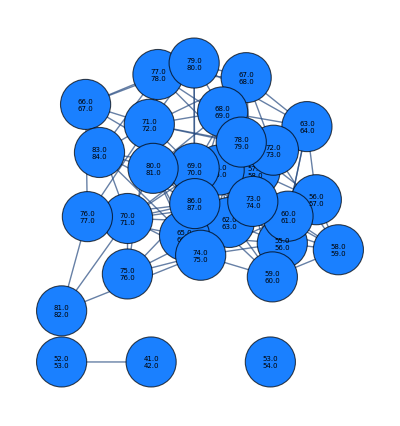
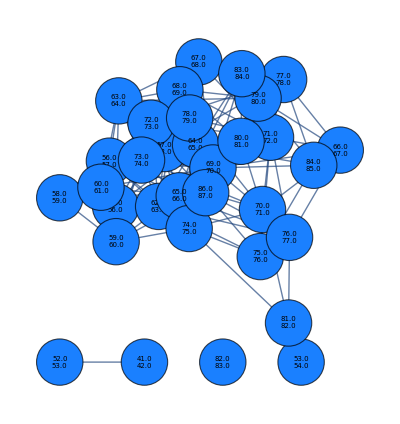
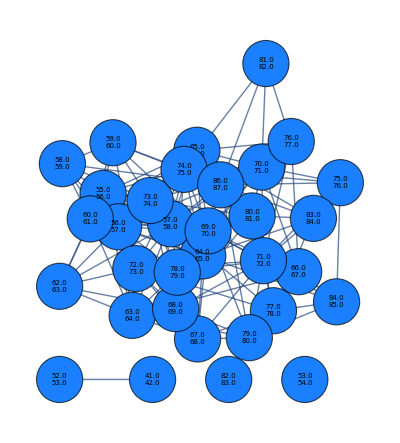
{{-Graphics-,25},{-Graphics-,27},{-Graphics-,27},{-Graphics-,27},{-Graphics-,30},{-Graphics-,31},{-Graphics-,33},{-Graphics-,33},{-Graphics-,35},{-Graphics-,35}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{88.2034,{{2.37693,4.83112,-5.89498},{2.97145,4.01518,-7.68207},{2.24826,2.72482,-8.07662},{2.60928,3.17294,-9.66783},{-0.350065,0.589557,-10.2151},{-0.15829,ComplexInfinity,-9.61058},{1.20069,ComplexInfinity,-9.94618},{0.540918,ComplexInfinity,-8.18174},{2.417,ComplexInfinity,-13.261},{3.97959,ComplexInfinity,-8.94487}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,4,4,4,4,4,6,5,5,4}

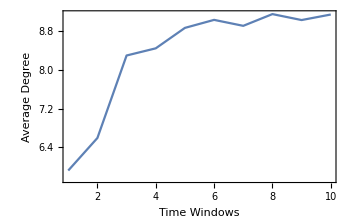
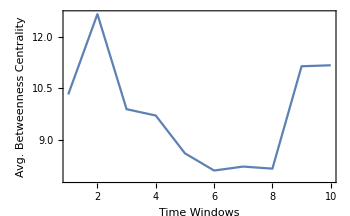
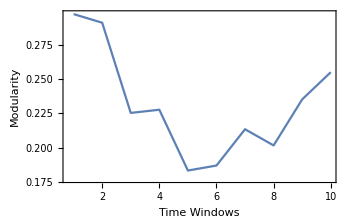
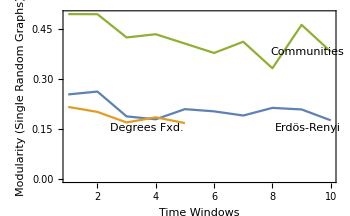
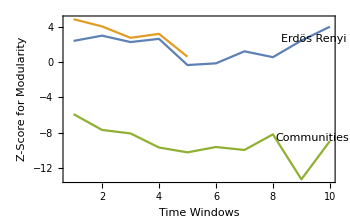

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,400,10];]
```

{343.177,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

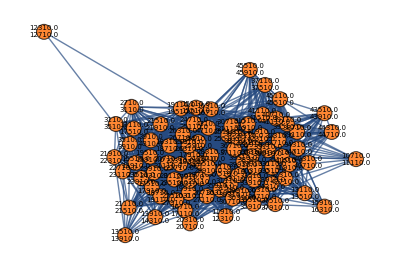
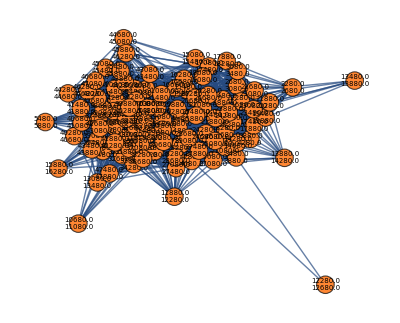
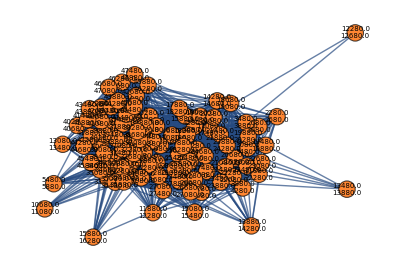
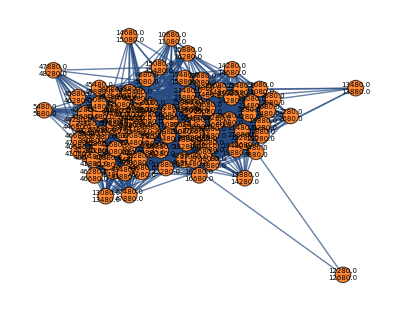
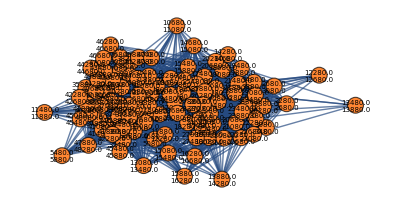
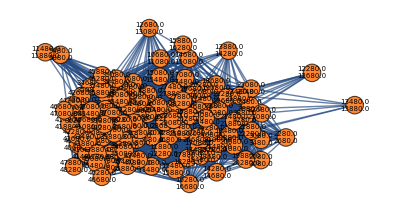
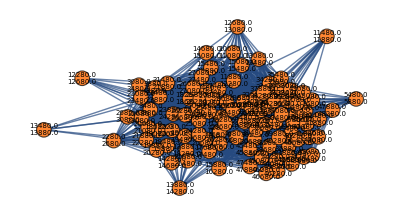
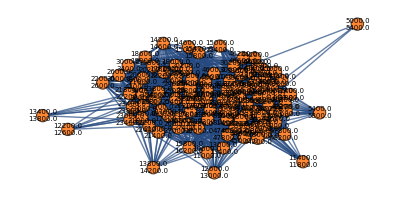
{{-Graphics-,84},{-Graphics-,96},{-Graphics-,96},{-Graphics-,98},{-Graphics-,99},{-Graphics-,100},{-Graphics-,100},{-Graphics-,101},{-Graphics-,102},{-Graphics-,102}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{514.225,{{35.5027,45.6529,-75.2784},{35.7657,49.3492,-93.909},{47.9151,62.9435,-86.0859},{50.892,65.4406,-90.5517},{54.5194,67.8051,-89.2524},{53.6673,63.9796,-87.4239},{53.8539,65.5125,-96.9836},{52.0831,65.5071,-91.3072},{51.9669,66.178,-94.0622},{52.1176,65.1834,-92.5287}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

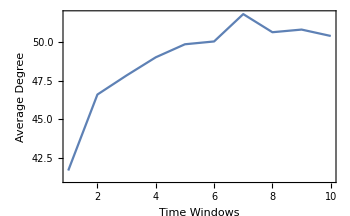
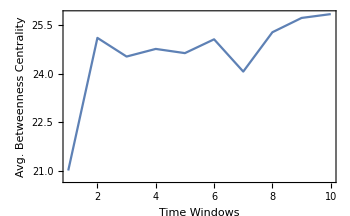
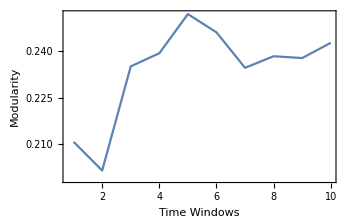
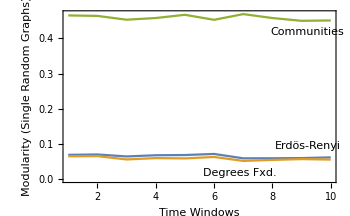
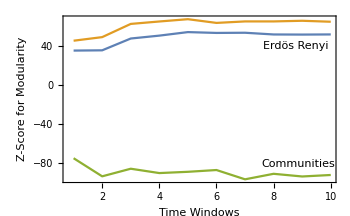

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,200,10];]
```

{421.01,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@10}];
```

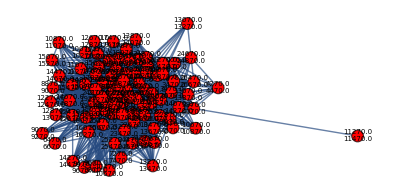
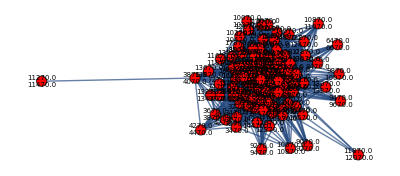
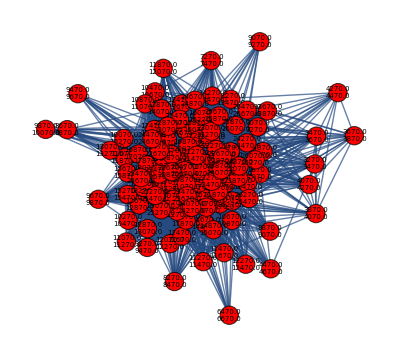
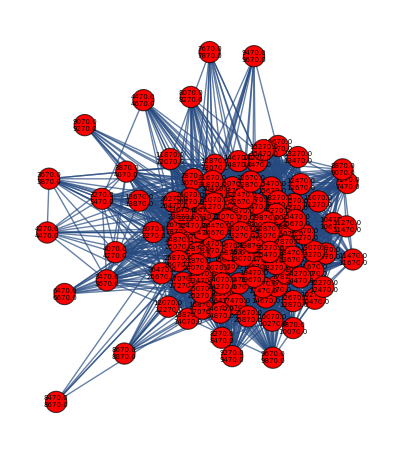
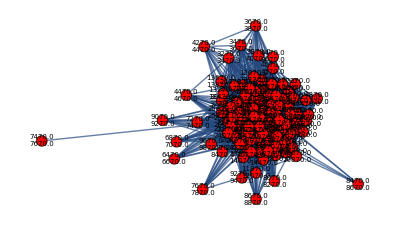
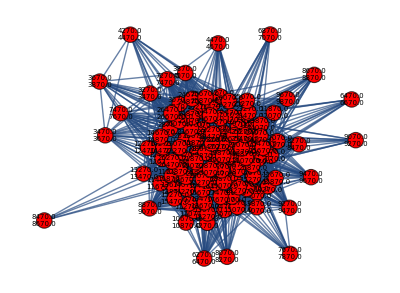
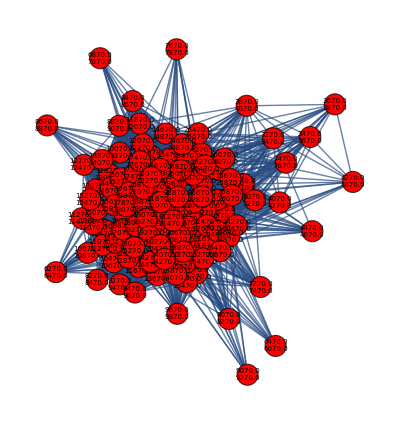
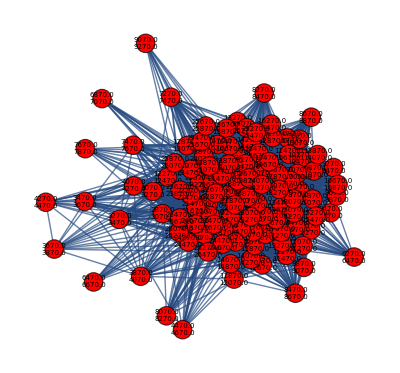
{{-Graphics-,94},{-Graphics-,101},{-Graphics-,103},{-Graphics-,106},{-Graphics-,108},{-Graphics-,109},{-Graphics-,109},{-Graphics-,109},{-Graphics-,110},{-Graphics-,110}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}]; (*IGraphM error: cannot shuffle graph, maybe there is only a single one?*)
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]](*IGraphM error: cannot shuffle graph, maybe there is only a single one?*)
```

{1577.14,{{7.38132,14.3776,-78.5669},{2.62395,9.42857,-129.783},{0.342742,6.34337,-157.182},{0.970574,7.30221,-164.736},{0.916458,7.99482,-137.731},{0.745323,7.57241,-164.481},{3.95656,12.1469,-157.392},{5.31554,13.836,-164.918},{6.11261,14.5838,-178.072},{7.01174,16.1961,-173.569}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,2,3,3,3,3,3,3,2,2}

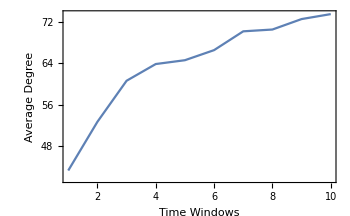
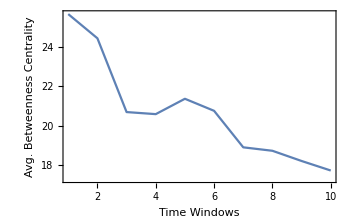
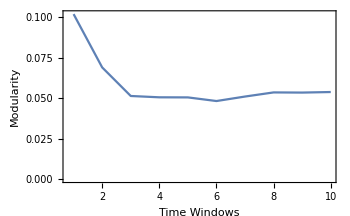
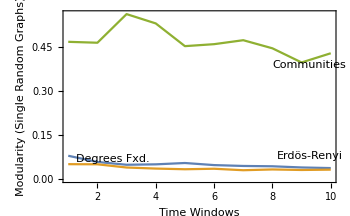
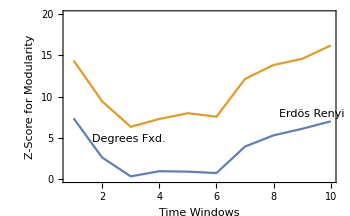
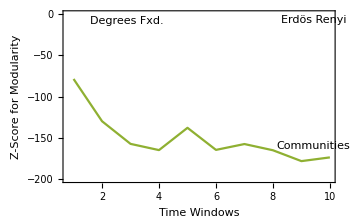

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{All,{0,20}},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{All,{-200,0}},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,85,10];]
```

{42.7637,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

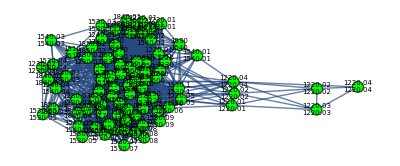
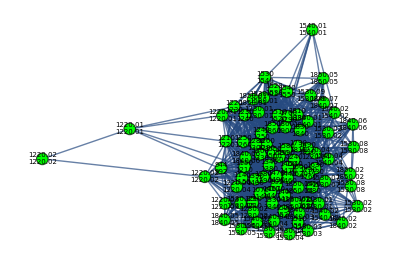
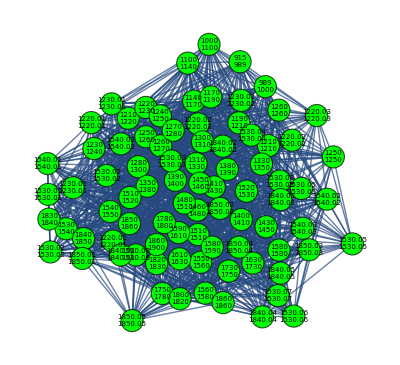
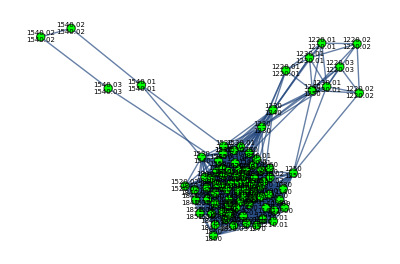
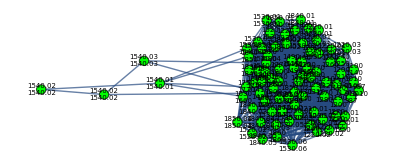
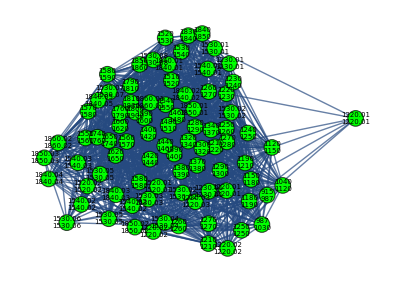
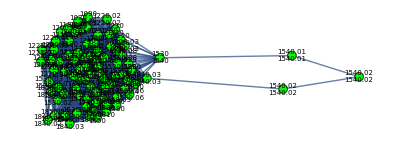
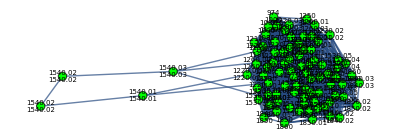
{{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85},{-Graphics-,85}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{316.444,{{17.5431,23.9292,-67.6722},{20.5186,25.7374,-70.4002},{17.627,19.0769,-71.7022},{9.60764,16.5075,-70.0018},{20.8851,25.1707,-66.6518},{23.3041,27.4286,-73.9713},{18.5205,22.8903,-82.4882},{28.1208,34.4891,-70.7885},{29.9387,31.6494,-70.0129},{26.9749,30.3644,-72.3368}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,3,3,3,3,3,2,2,3,2}

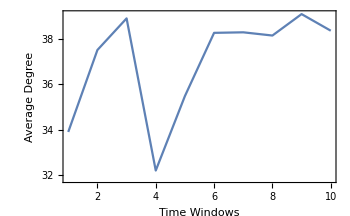
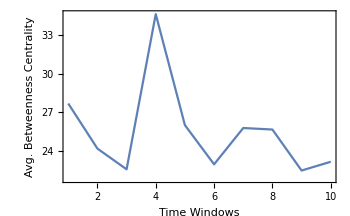
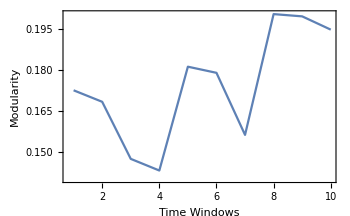
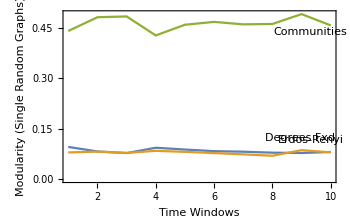
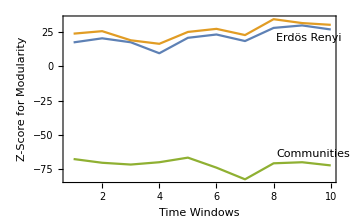

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,20,10];]
```

{93.5088,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

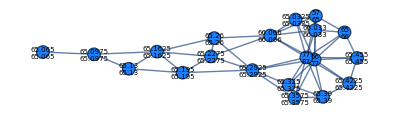
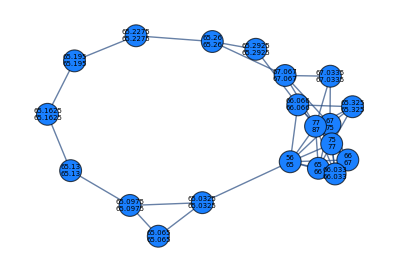
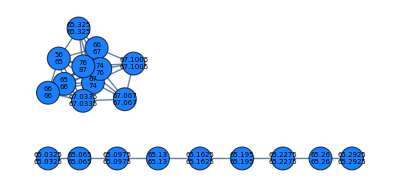
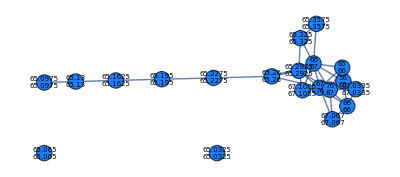
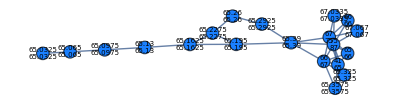
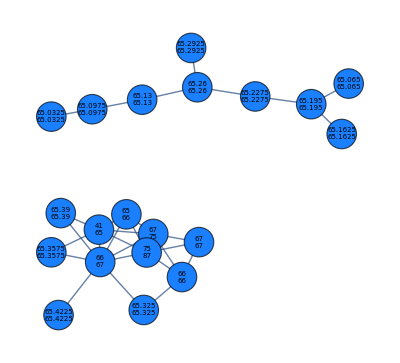
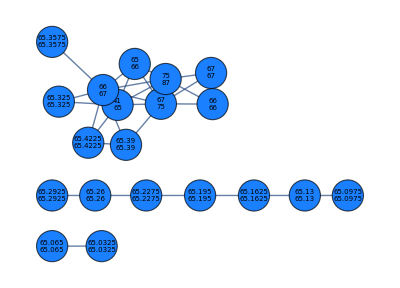
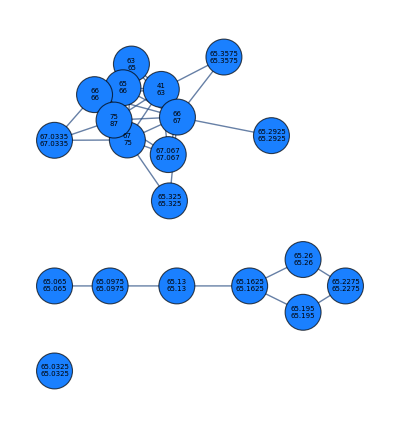
{{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20},{-Graphics-,20}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{80.3439,{{3.98547,5.36216,-4.10103},{1.09458,2.34283,-4.45779},{0.756882,3.48985,-0.49932},{0.67039,ComplexInfinity,-3.61341},{3.31431,4.48717,-3.67958},{0.726348,1.49886,-1.83612},{1.49655,2.94539,-3.26957},{-0.284126,ComplexInfinity,-1.68364},{1.27603,ComplexInfinity,-2.69577},{0.346461,ComplexInfinity,-2.50198}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,4,2,5,4,3,4,3,4,6}

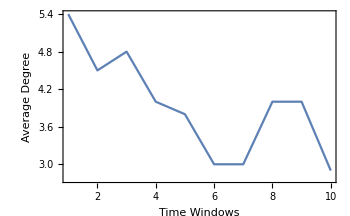
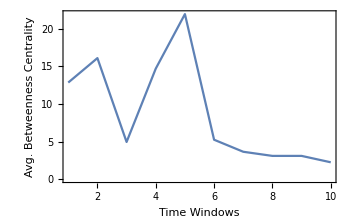
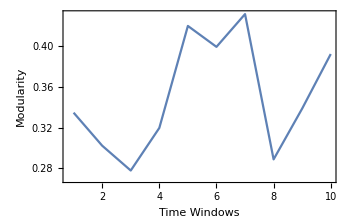
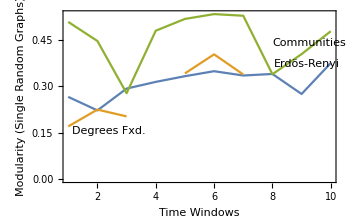
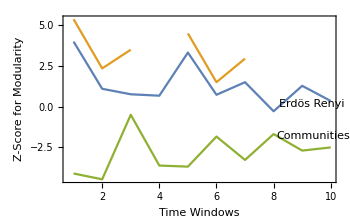

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,102,10];]
```

{44.0111,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

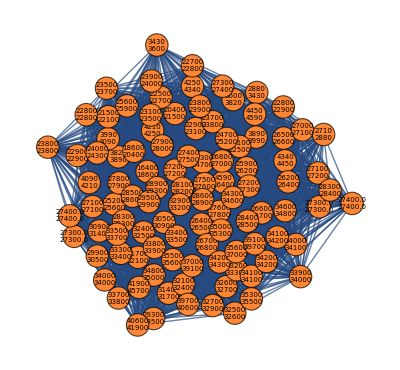
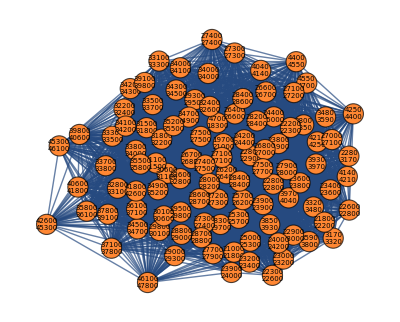
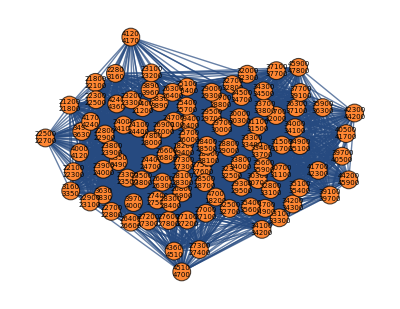
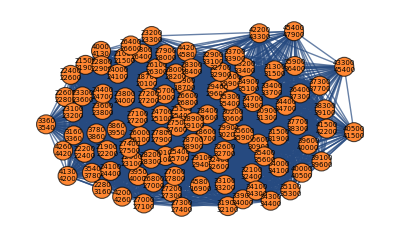
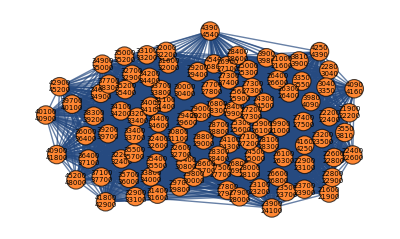
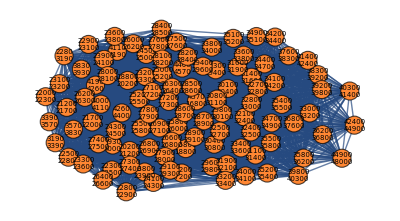
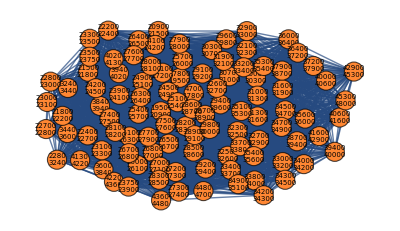
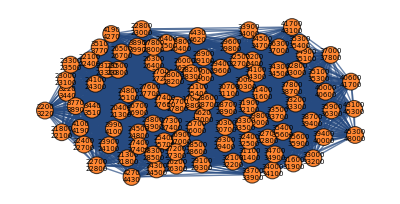
{{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102},{-Graphics-,102}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1607.08,{{18.6961,20.8245,-175.041},{36.2539,39.4034,-169.244},{55.0781,57.3735,-153.568},{60.774,62.3641,-155.029},{68.5138,74.3672,-151.76},{61.7652,69.9734,-166.583},{61.8676,67.1652,-168.518},{69.3002,75.2921,-150.362},{68.5226,74.7156,-154.95},{67.319,74.0693,-156.748}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

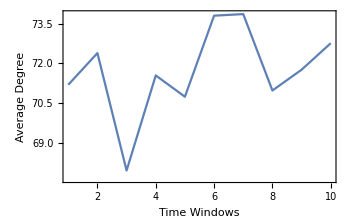
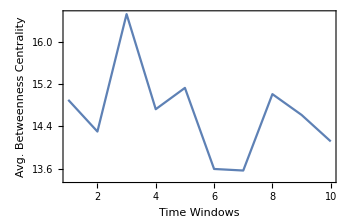
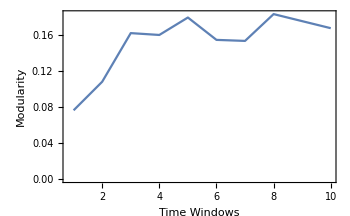
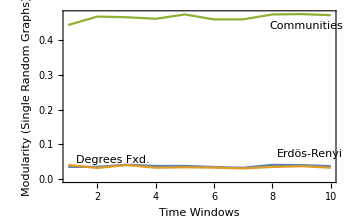
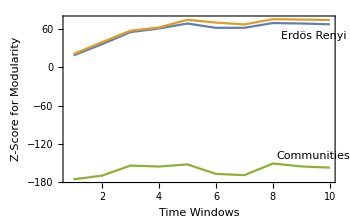

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,100,10];]
```

{45.2579,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@10}];
```

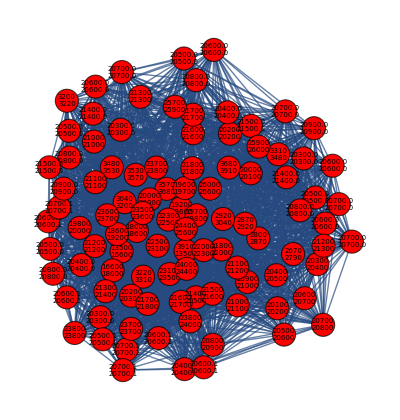
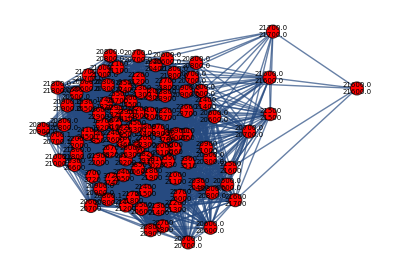
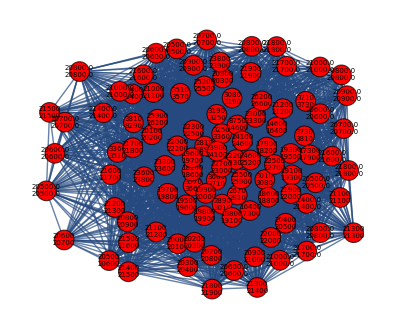
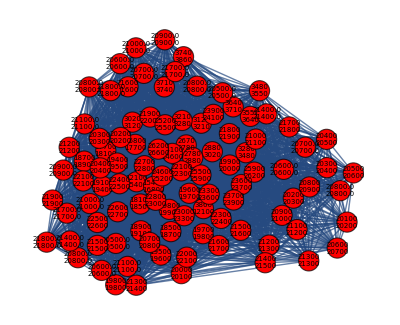
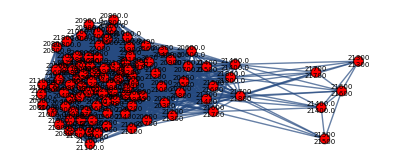
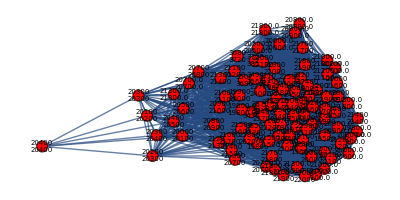
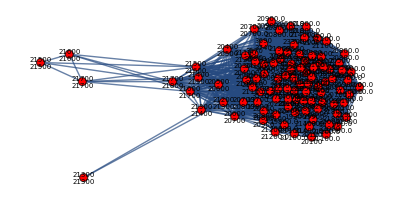
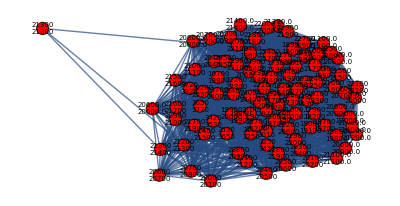
{{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100},{-Graphics-,100}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1419.47,{{35.5022,39.1606,-124.797},{28.2364,34.8486,-134.384},{28.2371,32.1491,-148.287},{41.7981,43.7248,-144.681},{31.5073,46.2941,-138.513},{31.3726,39.7919,-146.859},{27.7199,38.2688,-144.512},{33.1977,38.6974,-154.699},{38.5671,43.9159,-156.107},{25.0951,33.0398,-147.409}}}

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

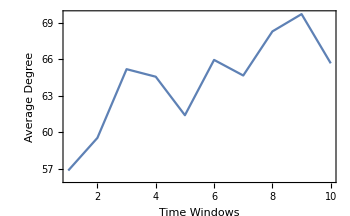
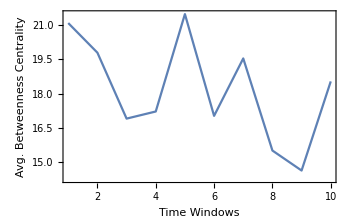
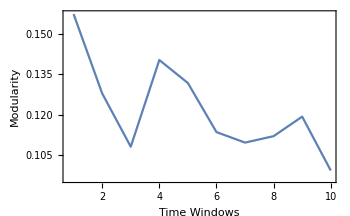
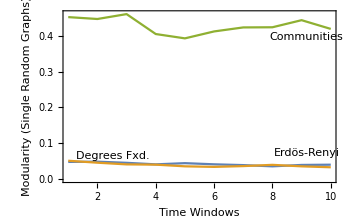
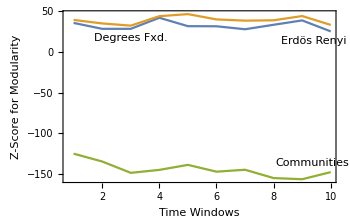

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->All],ListLinePlot[{Thread[{Range@10,singlerandomerdrenmodularityvalues}],Thread[{Range@10,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@10,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@10,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@10,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->All,PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Below}]]}
```